# Sample animation for the orbits of three very close initial conditions

Here we animate three orbits that have very close initial conditions but yield three different final states. We consider a particle initially in a circular orbit at ρ=3 with l>0 and b=0.2 shot at three different but very close shooting angles.

```mathematica
$IsPositive=True;MaximumT=10^6;
l[b_]:=If[$IsPositive,-3b+√(3+144 b^2),-3b-√(3+144 b^2)];
ddrho[b_] := ρ''[σ]==1/2(2ρ[σ]-3)(θ'[σ])^2+(2l[b]b-1)/(2 ρ[σ]^2)+(l[b]^2(2ρ[σ]-3))/(2 ρ[σ]^4 Sin[θ[σ]]^2)-b^2/2(2ρ[σ]-1)Sin[θ[σ]]^2
ddθ[b_]:= θ''[σ]==-2/ρ[σ]ρ'[σ]θ'[σ]+(l[b]^2 Cos[θ[σ]])/(ρ[σ]^4 Sin[θ[σ]]^3)-b^2 Sin[θ[σ]]Cos[θ[σ]]
dϕ[b_]:=ϕ'[σ]==l[b]/(ρ[σ]^2 Sin[θ[σ]]^2)-b
```

We obtain initial conditions using the getInitConditions function

```mathematica
getInitConditions[b_,en_,z_,ϕsh_]:=Module[{ρ0,θ0,Ueff,dρ0,dθ0,result},
ρ0=√(9+z^2);
θ0=ArcTan[z,3];
Ueff=(1-1/ρ0)(1+((l[b]-b (ρ0 Sin[θ0])^2)^2)/(ρ0 Sin[θ0])^2);
dρ0=(√((en^2-Ueff)/(Cos[θ0-ϕsh]^2+ρ0(ρ0-1)Sin[θ0-ϕsh]^2)))Cos[θ0-ϕsh];
dθ0=-(√((en^2-Ueff)/(Cos[θ0-ϕsh]^2+ρ0(ρ0-1)Sin[θ0-ϕsh]^2)))Sin[θ0-ϕsh];
result={ρ0,dρ0,θ0,dθ0}
];
```

We check the final state using the CheckAttractor function: (z > 1000) → 1, (z < -1000) → 2, (ρ ≤ 1) → 3 and (σ >MaximumT) → 4

```mathematica
Attractors = {WhenEvent[ρ[σ]Cos[θ[σ]]>1000,Throw[1]],WhenEvent[ρ[σ]Cos[θ[σ]]<-1000,Throw[2]],WhenEvent[ρ[σ]≤ 1,Throw[3]],WhenEvent[σ>MaximumT,Throw[4]]};
CheckAttractor[b_,en_,z_,ϕsh_]:=Module[{initConditions},
initConditions=getInitConditions[b,en,z,ϕsh];
Catch[
NDSolve[{ddθ[b],ddrho[b],ρ[0]==initConditions⟦1⟧,ρ'[0]==initConditions⟦2⟧,θ[0]==initConditions⟦3⟧,θ'[0]==initConditions⟦4⟧}~Join~Attractors,{ρ,θ},{σ,0,MaximumT+1}];
]
];
```

We found that these values of the initial conditions (ρ_0,dρ_0,θ_0,dθ_0) correspond to three different final states. Here we obtain the initial conditions for the three trajectories that we will look at

```mathematica
{CheckAttractor[0.2,1.2,0,-(103 π)/125],CheckAttractor[0.2,1.2,0,-(207 π)/250],CheckAttractor[0.2,1.2,0,-(41 π)/50]}
```

{1,2,3}

```mathematica
{-(103 π)/125,-(207 π)/250,-(41 π)/50}//N
```

{-2.58867,-2.60124,-2.57611}

We see that the shooting angles are very close to each other. We will see later that these shooting angle differences lead to radically different trajectories.

```mathematica
escapePlusInitConds=getInitConditions[0.2,1.2,0,-(103 π)/125](*Trajectory that will escape to positive infinity*)
escapeMinusInitConds=getInitConditions[0.2,1.2,0,-(207 π)/250](*Trajectory that will escape to negative infinity*)
captureInitConds=getInitConditions[0.2,1.2,0,-(41 π)/50](*Trajectory that will be captured*)
```

{3,-0.211595,π/2,0.342869}

{3,-0.206029,π/2,0.343433}

{3,-0.217219,π/2,0.342282}

We solve the differential equations for the different initial conditions.

```mathematica
solEscPlus=NDSolve[{ddrho[0.2],ddθ[0.2],ρ[0]==escapePlusInitConds⟦1⟧,ρ'[0]== escapePlusInitConds⟦2⟧,θ[0]== escapePlusInitConds⟦3⟧,θ'[0]== escapePlusInitConds⟦4⟧,WhenEvent[ρ[σ]Cos[θ[σ]]>1000,endEscPlus=σ;"StopIntegration"],WhenEvent[ρ[σ]Cos[θ[σ]]<-1000,endEscPlus=σ;"StopIntegration"],WhenEvent[ρ[σ]≤1,endEscPlus=σ;"StopIntegration"]},{ρ,θ,ϕ},{σ,0,MaximumT+1}];
solEscMinus=NDSolve[{ddrho[0.2],ddθ[0.2],ρ[0]==escapeMinusInitConds⟦1⟧,ρ'[0]== escapeMinusInitConds⟦2⟧,θ[0]== escapeMinusInitConds⟦3⟧,θ'[0]== escapeMinusInitConds⟦4⟧,WhenEvent[ρ[σ]Cos[θ[σ]]>1000,endEscMinus=σ;"StopIntegration"],WhenEvent[ρ[σ]Cos[θ[σ]]<-1000,endEscMinus=σ;"StopIntegration"],WhenEvent[ρ[σ]≤1,endEscMinus=σ;"StopIntegration"]},{ρ,θ,ϕ},{σ,0,MaximumT+1}];
solCapture=NDSolve[{ddrho[0.2],ddθ[0.2],ρ[0]==captureInitConds⟦1⟧,ρ'[0]== captureInitConds⟦2⟧,θ[0]== captureInitConds⟦3⟧,θ'[0]== captureInitConds⟦4⟧,WhenEvent[ρ[σ]Cos[θ[σ]]>1000,endCapture=σ;"StopIntegration"],WhenEvent[ρ[σ]Cos[θ[σ]]<-1000,endCapture=σ;"StopIntegration"],WhenEvent[ρ[σ]≤1,endCapture=σ;"StopIntegration"]},{ρ,θ,ϕ},{σ,0,MaximumT+1}];
```

```mathematica
solEscPlusPhi=NDSolve[{dϕ[0.2]/.solEscPlus,ϕ[0]==0},ϕ,{σ,0,endEscPlus}];
solEscMinusPhi=NDSolve[{dϕ[0.2]/.solEscMinus,ϕ[0]==0},ϕ,{σ,0,endEscMinus}];
solCapturePhi=NDSolve[{dϕ[0.2]/.solCapture,ϕ[0]==0},ϕ,{σ,0,endCapture}];
```

```mathematica
{endEscPlus,endEscMinus,endCapture}
```

{2431.02,2621.71,349.433}

We see that the capture trajectory took the longest to finish, while the positive escape trajectory finished the fastest. Next we make functions {x[σ],y[σ],z[σ]} for each solution to the differential equations.

```mathematica
xEscPlus[σ_]=ρ[σ]Sin[θ[σ]]Cos[ϕ[σ]]/.First@solEscPlus/.First@solEscPlusPhi;
yEscPlus[σ_]=ρ[σ]Sin[θ[σ]]Sin[ϕ[σ]]/.First@solEscPlus/.First@solEscPlusPhi;
zEscPlus[σ_]=ρ[σ]Cos[θ[σ]]/.First@solEscPlus;
xEscMinus[σ_]=ρ[σ]Sin[θ[σ]]Cos[ϕ[σ]]/.First@solEscMinus/.First@solEscMinusPhi;
yEscMinus[σ_]=ρ[σ]Sin[θ[σ]]Sin[ϕ[σ]]/.First@solEscMinus/.First@solEscMinusPhi;
zEscMinus[σ_]=ρ[σ]Cos[θ[σ]]/.First@solEscMinus;
xCapture[σ_]=ρ[σ]Sin[θ[σ]]Cos[ϕ[σ]]/.First@solCapture/.First@solCapturePhi;
yCapture[σ_]=ρ[σ]Sin[θ[σ]]Sin[ϕ[σ]]/.First@solCapture/.First@solCapturePhi;
zCapture[σ_]=ρ[σ]Cos[θ[σ]]/.First@solCapture;
```

We look at the z(t) functions for the trajectories

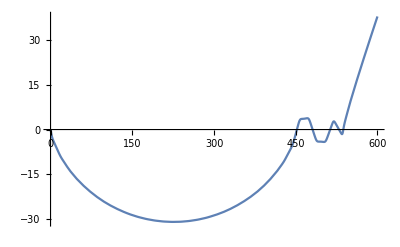

```mathematica
Plot[zEscPlus[t],{t,0,600}]
```

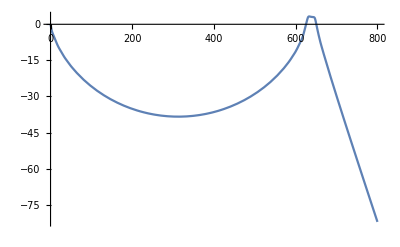

```mathematica
Plot[zEscMinus[t],{t,0,800}]
```

We see that the 1st particle goes to positive infinity at about t=600 while the 2nd particle goes to negative infinity at about t=800. Let’s also check the bounds on √((x(t))^2+(y(t))^2).

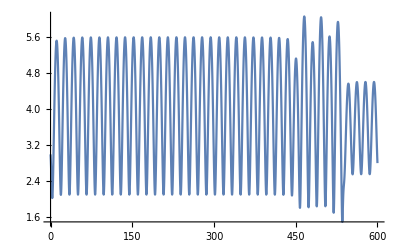

```mathematica
Plot[√(xEscPlus[t]^2+yEscPlus[t]^2),{t,0,600}]
```

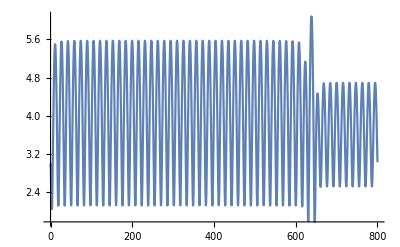

```mathematica
Plot[√(xEscMinus[t]^2+yEscMinus[t]^2),{t,0,800}]
```

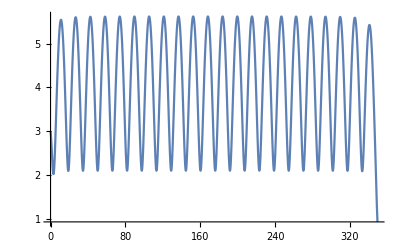

```mathematica
Plot[√(xCapture[t]^2+yCapture[t]^2),{t,0,endCapture}]
```

We see that the orbits are safely bounded by a cylindrical radius of 6.5.

```mathematica
Show[ParametricPlot3D[{xEscPlus[t],yEscPlus[t],zEscPlus[t]},{t,0,800},PlotStyle->{Yellow,Thin},PlotRange->{{-6.5,6.5},{-6.5,6.5},{-35,35}},AspectRatio->Automatic],Graphics3D[{Gray,Sphere[{0,0,0}]}],ImageSize->300]
```

-Graphics3D-

```mathematica
Show[ParametricPlot3D[{xEscMinus[t],yEscMinus[t],zEscMinus[t]},{t,0,800},PlotStyle->{Blue,Thin},PlotRange->{{-6.5,6.5},{-6.5,6.5},{-35,35}},AspectRatio->Automatic],Graphics3D[{Gray,Sphere[{0,0,0}]}],ImageSize->300]
```

-Graphics3D-

```mathematica
Show[ParametricPlot3D[{xCapture[t],yCapture[t],zCapture[t]},{t,0,endCapture},PlotStyle->{Red,Thin},PlotRange->{{-6.5,6.5},{-6.5,6.5},{-30,30}},AspectRatio->Automatic],Graphics3D[{Gray,Sphere[{0,0,0}]}],ImageSize->300]
```

-Graphics3D-

## Making the animation

We allot 150 frames for the first t=349 seconds of the animation (until one of the particles is captured) and then another 150 frames for the rest of the animation until t=800.

```mathematica
tRange1=Subdivide[0,349,149];
tRange2=Subdivide[350,800,149];
```

```mathematica
movieVector=ConstantArray[0,Length[tRange1~Join~tRange2]];
```

```mathematica
Length[movieVector]
```

300

All in all we have 300 frames. Next we denote (x_p,y_p,z_p), (x_m,y_m,z_m), (x_c,y_c,z_c) the coordinates of the z→ +∞, z→ -∞, and captured trajectories respectively. We first render the first 150 frames.

```mathematica
For[k=1,k≤150,k++,
tk=tRange1⟦k⟧;

(*Coordinates of the z->+∞ trajectory*)
xpk=xEscPlus[tk];
ypk=yEscPlus[tk];
zpk=zEscPlus[tk];

(*Coordinates of the z->-∞ trajectory*)
xmk=xEscMinus[tk];
ymk=yEscMinus[tk];
zmk=zEscMinus[tk];

(*Coordinates of the captured trajectory*)
xck=xCapture[tk];
yck=yCapture[tk];
zck=zCapture[tk];

movieVector⟦k⟧=Show[
(*Plot of the z->+∞ trajectory*)
ParametricPlot3D[{xEscPlus[t],yEscPlus[t],zEscPlus[t]},{t,Max[0,tk-50],Max[0.1,tk]},PlotStyle->{Yellow,Thin},PlotRange->{{-6.5,6.5},{-6.5,6.5},{-40,40}},AspectRatio->Automatic,Axes->None,Boxed->False],

(*Plot of the z->-∞ trajectory*)
ParametricPlot3D[{xEscMinus[t],yEscMinus[t],zEscMinus[t]},{t,Max[0,tk-50],Max[0.1,tk]},PlotStyle->{Blue,Thin},PlotRange->{{-6.5,6.5},{-6.5,6.5},{-40,40}},AspectRatio->Automatic,Axes->None,Boxed->False],

(*Plot of the captured trajectory*)
ParametricPlot3D[{xCapture[t],yCapture[t],zCapture[t]},{t,Max[0,tk-50],Max[0.1,tk]},PlotStyle->{Red,Thin},PlotRange->{{-6.5,6.5},{-6.5,6.5},{-40,40}},AspectRatio->Automatic,Axes->None,Boxed->False],

(*Gray sphere representing the black hole*)
Graphics3D[{Gray,Sphere[{0,0,0}]}],

(*Yellow dot on position of z->+∞ particle*)
Graphics3D[
{
AbsolutePointSize[10],Yellow,Point[{xpk,ypk,zpk}]
}
],

(*Blue dot on position of z->-∞ particle*)
Graphics3D[
{
AbsolutePointSize[10],Blue,Point[{xmk,ymk,zmk}]
}
],

(*Red dot on position of captured particle*)
Graphics3D[
{
AbsolutePointSize[10],Red,Point[{xck,yck,zck}]
}
],

(*Other designs on the plot*)
ImageSize->300,
PlotLabel->StringJoin["b=0.2, l≃2.36: t = ",ToString[N[tk]]],
LabelStyle->{FontSize->14}

]
];
```

Next we render the last 150 frames.

```mathematica
For[k=1,k≤150,k++,
tk=tRange2⟦k⟧;

(*Coordinates of the z->+∞ trajectory*)
xpk=xEscPlus[tk];
ypk=yEscPlus[tk];
zpk=zEscPlus[tk];

(*Coordinates of the z->-∞ trajectory*)
xmk=xEscMinus[tk];
ymk=yEscMinus[tk];
zmk=zEscMinus[tk];

(*Coordinates of the captured trajectory*)
xck=xCapture[endCapture];
yck=yCapture[endCapture];
zck=zCapture[endCapture];

movieVector⟦k+150⟧=Show[
(*Plot of the z->+∞ trajectory*)
ParametricPlot3D[{xEscPlus[t],yEscPlus[t],zEscPlus[t]},{t,Max[0,tk-50],Max[0.1,tk]},PlotStyle->{Yellow,Thin},PlotRange->{{-6.5,6.5},{-6.5,6.5},{-40,40}},AspectRatio->Automatic,Axes->None,Boxed->False],

(*Plot of the z->-∞ trajectory*)
ParametricPlot3D[{xEscMinus[t],yEscMinus[t],zEscMinus[t]},{t,Max[0,tk-50],Max[0.1,tk]},PlotStyle->{Blue,Thin},PlotRange->{{-6.5,6.5},{-6.5,6.5},{-40,40}},AspectRatio->Automatic,Axes->None,Boxed->False],

(*Plot of the captured trajectory*)
ParametricPlot3D[{xCapture[t],yCapture[t],zCapture[t]},{t,Min[tk-50,endCapture-0.1],endCapture},PlotStyle->{Red,Thin},PlotRange->{{-6.5,6.5},{-6.5,6.5},{-40,40}},AspectRatio->Automatic,Axes->None,Boxed->False],

(*Gray sphere representing the black hole*)
Graphics3D[{Gray,Sphere[{0,0,0}]}],

(*Yellow dot on position of z->+∞ particle*)
Graphics3D[
{
AbsolutePointSize[10],Yellow,Point[{xpk,ypk,zpk}]
}
],

(*Blue dot on position of z->-∞ particle*)
Graphics3D[
{
AbsolutePointSize[10],Blue,Point[{xmk,ymk,zmk}]
}
],

(*Red dot on position of captured particle*)
Graphics3D[
{
AbsolutePointSize[10],Red,Point[{xck,yck,zck}]
}
],

(*Other designs on the plot*)
ImageSize->300,
PlotLabel->StringJoin["b=0.2, l≃2.36: t = ",ToString[N[tk]]],
LabelStyle->{FontSize->14}

]
]
```

We save the rendered frames as an “avi” file located in

```mathematica
Directory[]
```

E:\Joshua\Documents

using the command

```mathematica
Export["ChaoticTrajectory.avi",movieVector]
```

ChaoticTrajectory.avi